```mathematica
csv = Import["C:\\Users\\Rub Abella\\Google Drive\\Lecture-Notes-And-Resources\\CMSC 56\\asymptotic analysis example algorithms\\scores3.csv","Data"];
```

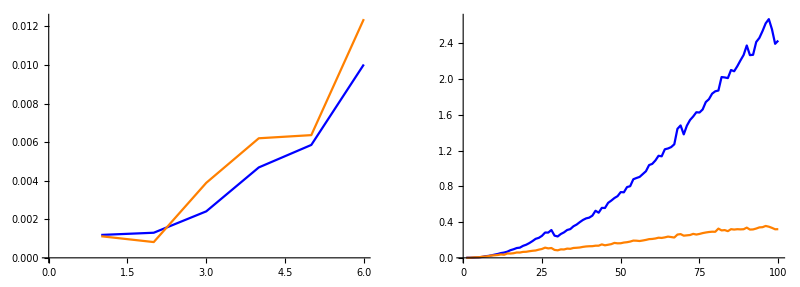

```mathematica
csvlite = csv[[1;;6]];
g2 = ListLinePlot[Transpose[csv],PlotStyle-> {Blue,Orange}];
g1 = ListLinePlot[Transpose[csvlite],PlotStyle-> {Blue,Orange}];
GraphicsGrid[{{g1,g2,LineLegend[{Blue,Orange},{"Bubble Sort", "Merge Sort"}]}},ImageSize->Full]
```

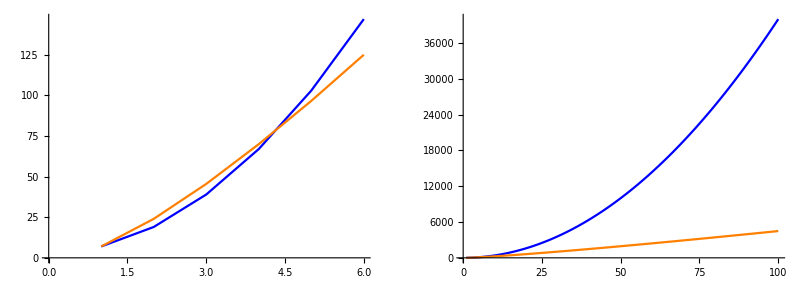

```mathematica
g1 =ListLinePlot[Transpose[Table[{4 n^2+3,6n Log[2,n] +5n + 2},{n,1,6}]],PlotStyle->{Blue,Orange}];
g2 =ListLinePlot[Transpose[Table[{4 n^2+3,6n Log[2,n] +5n + 2},{n,1,100}]],PlotStyle->{Blue,Orange}];
GraphicsGrid[{{g1,g2,LineLegend[{Blue,Orange},{"Bubble Sort", "Merge Sort"}]}},ImageSize->Full]
```